# The Energy Function of ^163 Lu

## Computing the Energy Function ℋ(I,θ,φ) for the nucleus

## ℋ=I/2(A_1+A_2)+A_3 I^2+I(I-1/2)sin^2 θ(A_1 cos^2 φ+A_2 sin^2 φ-A_3)+j/2(A_2+A_3)+A_1 j^2-2 A_1 Ij sinθ-V(2j-1)/(j+1)sin(γ+π/6);

### Constants (deformation parameters from actual fit)

```mathematica
A1=1/(2*73);
A2=1/(2*3);
A3=1/(2*67);
V=6.01;
j=13/2;
γ=21;
spinTSD1=25/2;
spinTSD2=31/2;
spinTSD3=37/2;
spinTSD4=51/2;
```

### Expression

```mathematica
Hen[I_,θ_,φ_]:=I/2(A1+A2)+A3*I^2+I(I-1/2)Sin[θ*π/180]^2(A1*Cos[φ*π/180]^2+A2*Sin[φ*π/180]^2-A3)+j/2(A2+A3)+A1*j^2-2A1*I*j*Sin[θ*π/180]-V*(2j-1)/(j+1)Sin[γ*π/180+π/6];
```

```mathematica
p1[spin_]:=ContourPlot[{Hen[spin,θ,φ]},{θ,0,180},{φ,0,360},Frame->True,FrameStyle->Directive[Black,Thick],Contours->8,FrameLabel->{"θ","φ"},PlotLabel->StringTemplate["I=``"][spin],LabelStyle->{15,Black,Bold,FontFamily->"Times New Roman"},ImageSize->Medium,AspectRatio->Automatic,PlotLegends->Automatic];
Show[p1[spinTSD1]]
(*Save the graph with the Contour Plot to an output file*)
(*Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Reports/ContourPlot1.jpeg",pf];*)
```

-Graphics-

## Plots

```mathematica
Show[p1[spinTSD1]]
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Reports/ContourPlot1.pdf",p1[spinTSD1]];
```

-Graphics-

```mathematica
Show[p1[spinTSD2]]
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Reports/ContourPlot2.pdf",p1[spinTSD2]];
```

-Graphics-

```mathematica
Show[p1[spinTSD3]]
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Reports/ContourPlot3.pdf",p1[spinTSD3]];
```

-Graphics-

```mathematica
Show[p1[spinTSD4]]
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Reports/ContourPlot4.pdf",p1[spinTSD4]];
```

-Graphics-

-Graphics-

## Graphics Grid with all the spins for the bands

```mathematica
pf=GraphicsGrid[{{Show[p1[spinTSD1]],Show[p1[spinTSD2]]},{Show[p1[spinTSD3]],Show[p1[spinTSD4]]}}];
```

## Computing the first and second derivatives of H

```mathematica
difH1[q_]:=N[D[Hen[spinTSD1,θ,φ],θ]/.{θ->q}];
difH2[q_]:=N[D[Hen[spinTSD1,θ,φ],φ]/.{φ->q}];
diffH1[q_]:=N[D[Hen[spinTSD1,θ,φ],{θ,2}]/.{θ->q}];
diffH2[q_]:=N[D[Hen[spinTSD1,θ,φ],{φ,2}]/.{φ->q}];
```

```mathematica
N[Hen[spinTSD1,50,10.648054173771346]]
```

-4.79352

```mathematica
Show[ContourPlot[{Hen[spinTSD1,θ,φ]},{θ,0,180},{φ,0,360},Frame->True,FrameStyle->Directive[Black,Thick],Contours->8,FrameLabel->{"θ","φ"},PlotLabel->StringTemplate["I=``"][spinTSD1],LabelStyle->{15,Black,Bold,FontFamily->"Times New Roman"},ImageSize->Medium,AspectRatio->Automatic,PlotLegends->Automatic],ContourPlot[{Hen[spinTSD1,θ,φ]==-5.572231367},{θ,0,180},{φ,0,360},Contours->2,ContourStyle->Red]]
```

-Graphics-

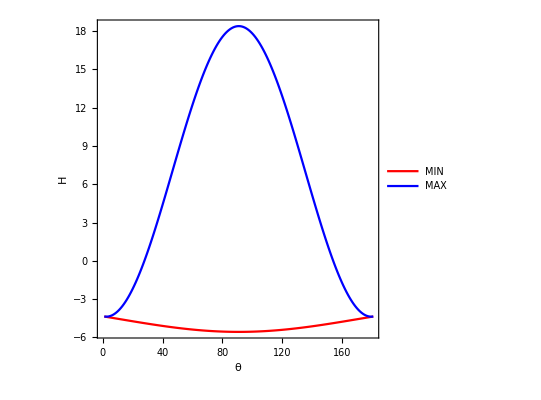

```mathematica
findmin[θ_]:=FindMinimum[{Hen[spinTSD1,θ,φ],0≤φ≤180},{φ}];
findmax[θ_]:=FindMaximum[{Hen[spinTSD1,θ,φ],0≤φ≤180},{φ}];
mylistmin=Table[findmin[th][[1]],{th,0,180,1}];
mylistmax=Table[findmax[th][[1]],{th,0,180,1}];
ListPlot[{mylistmin,mylistmax},Frame->True,Axes->False,AspectRatio->1,Joined->True,PlotMarkers->None,FrameStyle->Directive[Black,Thick],FrameLabel->{"θ","H"},PlotLegends->{"MIN","MAX"},PlotStyle->{{Red,Thick},{Blue,Thick}},LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"}]
```